```mathematica
Solve[Exp[x]==1,x]
```

{{x→ConditionalExpression[2 ⅈ π C[1],C[1]∈Integers]}}

```mathematica
∫_0^(√2) x^3 ⅆx
```

1

```mathematica
(2 √2)/3//N
```

0.942809

```mathematica
∫_(-∞)^0 Exp[x]ⅆx
```

1

```mathematica
∫_(-∞)^0 x Exp[x]ⅆx
```

-1

```mathematica
∫_(-∞)^0 x^2 Exp[x]ⅆx
```

2

```mathematica
∫_0^1 Exp[x]ⅆx//N
```

1.71828

```mathematica
f[x_]:= Exp[0.4(x-0.4)^2-0.08 x^4]
```

```mathematica
Q1[x_,s_]:=√(1/(2π s^2))Exp[-x^2/(2 s^2)]
```

```mathematica
∫_-5^5 10*Q1[x,1]ⅆx//N
```

9.99999

```mathematica
Clear[x]
```

```mathematica
∫10*Q1[x,0.1]ⅆx
```

5. Erf[7.07107 x]

```mathematica
Solve[5 Erf[x/(√2)]==y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→√2 InverseErf[y/5]}}

```mathematica
Solve[5 Erf[x/(√2)]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0}}

```mathematica
Solve[5 Erf[x/(√2)]==1,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{{x->√2 InverseErf[1/5]}}//N
```

{{x→0.253347}}

```mathematica
u=RandomReal[1,100000]//N;
```

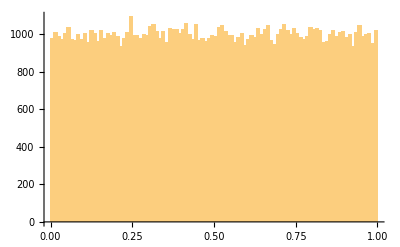

```mathematica
Histogram[u,100]
```

```mathematica
u[[100000]]
```

0.96298

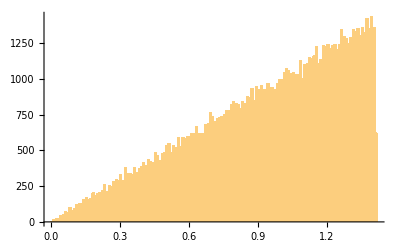

```mathematica
Histogram[√(2u),100]
```

```mathematica
x=RandomReal[1,10]//N
```

{0.95572,0.617615,0.871635,0.840679,0.876712,0.288603,0.435311,0.850133,0.151703,0.803568}

```mathematica
Sum[√(2u)[[i]],{i,1,1000}]//N
```

933.026

```mathematica
x=RandomReal[{-1,1},100000];
```

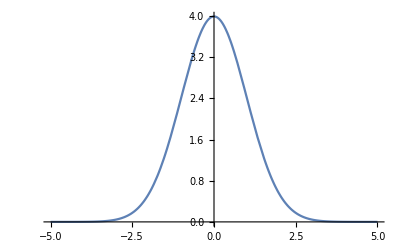

```mathematica
Plot[10Q1[x,1],{x,-5,5}]
```

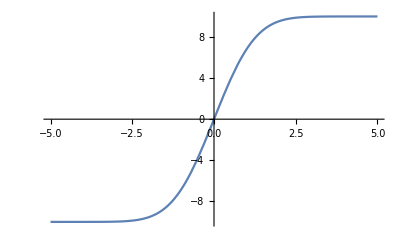

```mathematica
Plot[10Erf[x/(√2)],{x,-5,5}]
```

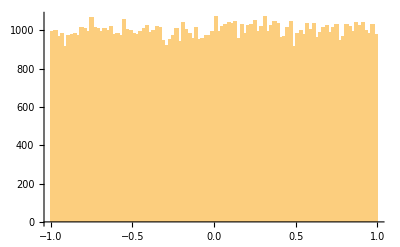

```mathematica
Histogram[ x,100]
```

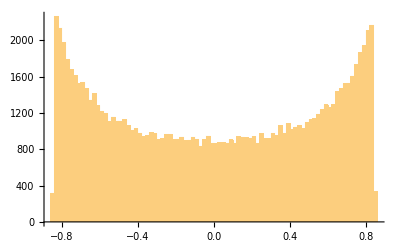

```mathematica
Histogram[ Erf[x],100]
```

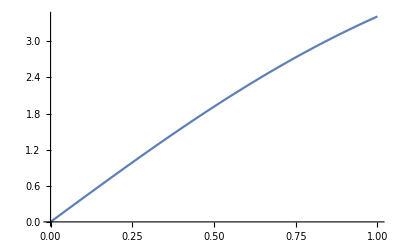

```mathematica
Plot[5 Erf[x/(√2)],{x,0,1}]
```